Accuracy study
This is an accuaracy study based on John L.Gustafson experiments to compare Floats vs.Posits

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "PositUtils.m"}]]
Get[FileNameJoin[{NotebookDirectory[], "FloatUtils.m"}]]
```

## 6 Floats vs.Posits Preview : Accuracy on a 32 - bit budget

If we evaluate the expression  ((27/10-ⅇ)/(π-(√2+√3)))^(67/16)correct to ten decimals, it is

```mathematica
z=((27/10-ⅇ)/(π-(√2+√3)))^(67/16);N[z, 11]
```

302.88271966

```mathematica
accbenchf:=Module[{te=UnderBar[ⅇ], t2710=UnderBar[27/10],tpi=UnderBar[Pi],tr2=UnderBar[Sqrt[2]], tr3=UnderBar[Sqrt[3]], tnum, t1,tden,t2,t6716,tans},
tnum=UnderBar[t2710-te];
t1=UnderBar[tr2+tr3];
tden=UnderBar[tpi-t1];
t2=UnderBar[tnum/tden];
t6716=UnderBar[67/16];
tans=UnderBar[t2^(t6716)];
Print[Style[Row[{"Float answer to ",nfbits-esize," decimals: "}],"Text"],N[tans,nfbits-esize]];
Print[Style["Rounding error in answer: ", "Text"],
N[z-tans]]
]
```

```mathematica
setfloatenv[{32,8}]
accbenchf
```

Float answer to 24 decimals: 302.91241455078125

Rounding error in answer: -0.0296949

```mathematica
accbenchp:=Module[{te=OverBar[ⅇ], t2710=OverBar[27/10],tpi=OverBar[Pi],tr2=OverBar[Sqrt[2]], tr3=OverBar[Sqrt[3]], tnum,tden,t2,t6716,tans},
tnum=OverBar[t2710-te];
tden=OverBar[tpi-(tr2+tr3)]; (*Posits allow this kind of fused operation*)
t2=OverBar[tnum/tden];
t6716=OverBar[67/16];
tans=OverBar[t2^(t6716)];
Print[Style[Row[{"Posit answer with es = ",es,": "}],"Text"],N[tans,nbits-es-9]];
Print[Style["Rounding error in answer: ", "Text"],
N[z-tans], "\n"]
]
```

```mathematica
For[i=0,i≤5,i++,setpositenv[{32,i}];accbenchp]
```

Posit answer with es = 0: 302.8817138671875

Rounding error in answer: 0.00100579

Posit answer with es = 1: 302.882781982421875

Rounding error in answer: -0.0000623271

Posit answer with es = 2: 302.88330078125

Rounding error in answer: -0.000581126

Posit answer with es = 3: 302.88231658935546875

Rounding error in answer: 0.000403066

Posit answer with es = 4: 302.888336181640625

Rounding error in answer: -0.00561653

Posit answer with es = 5: 302.872161865234375

Rounding error in answer: 0.0105578

## 7 Posits versus IEEE - type Floats : A Metric - Based Study

```mathematica
setfloatenv[{8,4}]
float8=Table[f2x[floatfix[f]],{f,0,2^(nfbits)-1}];
Table[TableForm[{float8[[i]]}],{i,1,Length[float8]}]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-∞,-240,-224,-208,-192,-176,-160,-144,-128,-120,-112,-104,-96,-88,-80,-72,-64,-60,-56,-52,-48,-44,-40,-36,-32,-30,-28,-26,-24,-22,-20,-18,-16,-15,-14,-13,-12,-11,-10,-9,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2,-15/8,-7/4,-13/8,-3/2,-11/8,-5/4,-9/8,-1,-15/16,-7/8,-13/16,-3/4,-11/16,-5/8,-9/16,-1/2,-15/32,-7/16,-13/32,-3/8,-11/32,-5/16,-9/32,-1/4,-15/64,-7/32,-13/64,-3/16,-11/64,-5/32,-9/64,-1/8,-15/128,-7/64,-13/128,-3/32,-11/128,-5/64,-9/128,-1/16,-15/256,-7/128,-13/256,-3/64,-11/256,-5/128,-9/256,-1/32,-15/512,-7/256,-13/512,-3/128,-11/512,-5/256,-9/512,-1/64,-7/512,-3/256,-5/512,-1/128,-3/512,-1/256,-1/512,0,0,1/512,1/256,3/512,1/128,5/512,3/256,7/512,1/64,9/512,5/256,11/512,3/128,13/512,7/256,15/512,1/32,9/256,5/128,11/256,3/64,13/256,7/128,15/256,1/16,9/128,5/64,11/128,3/32,13/128,7/64,15/128,1/8,9/64,5/32,11/64,3/16,13/64,7/32,15/64,1/4,9/32,5/16,11/32,3/8,13/32,7/16,15/32,1/2,9/16,5/8,11/16,3/4,13/16,7/8,15/16,1,9/8,5/4,11/8,3/2,13/8,7/4,15/8,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,9/2,5,11/2,6,13/2,7,15/2,8,9,10,11,12,13,14,15,16,18,20,22,24,26,28,30,32,36,40,44,48,52,56,60,64,72,80,88,96,104,112,120,128,144,160,176,192,208,224,240,∞,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
setpositenv[{8,1}]
{minpos,maxpos}
posit8=Table[p2x[positfix[j]],{j,0,npat-1}];
Table[TableForm[{posit8[[i]]}],{i,1,npat}]
```

{1/4096,4096}

{ComplexInfinity,-4096,-1024,-512,-256,-192,-128,-96,-64,-56,-48,-40,-32,-28,-24,-20,-16,-15,-14,-13,-12,-11,-10,-9,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-31/8,-15/4,-29/8,-7/2,-27/8,-13/4,-25/8,-3,-23/8,-11/4,-21/8,-5/2,-19/8,-9/4,-17/8,-2,-31/16,-15/8,-29/16,-7/4,-27/16,-13/8,-25/16,-3/2,-23/16,-11/8,-21/16,-5/4,-19/16,-9/8,-17/16,-1,-31/32,-15/16,-29/32,-7/8,-27/32,-13/16,-25/32,-3/4,-23/32,-11/16,-21/32,-5/8,-19/32,-9/16,-17/32,-1/2,-31/64,-15/32,-29/64,-7/16,-27/64,-13/32,-25/64,-3/8,-23/64,-11/32,-21/64,-5/16,-19/64,-9/32,-17/64,-1/4,-15/64,-7/32,-13/64,-3/16,-11/64,-5/32,-9/64,-1/8,-15/128,-7/64,-13/128,-3/32,-11/128,-5/64,-9/128,-1/16,-7/128,-3/64,-5/128,-1/32,-7/256,-3/128,-5/256,-1/64,-3/256,-1/128,-3/512,-1/256,-1/512,-1/1024,-1/4096,0,1/4096,1/1024,1/512,1/256,3/512,1/128,3/256,1/64,5/256,3/128,7/256,1/32,5/128,3/64,7/128,1/16,9/128,5/64,11/128,3/32,13/128,7/64,15/128,1/8,9/64,5/32,11/64,3/16,13/64,7/32,15/64,1/4,17/64,9/32,19/64,5/16,21/64,11/32,23/64,3/8,25/64,13/32,27/64,7/16,29/64,15/32,31/64,1/2,17/32,9/16,19/32,5/8,21/32,11/16,23/32,3/4,25/32,13/16,27/32,7/8,29/32,15/16,31/32,1,17/16,9/8,19/16,5/4,21/16,11/8,23/16,3/2,25/16,13/8,27/16,7/4,29/16,15/8,31/16,2,17/8,9/4,19/8,5/2,21/8,11/4,23/8,3,25/8,13/4,27/8,7/2,29/8,15/4,31/8,4,9/2,5,11/2,6,13/2,7,15/2,8,9,10,11,12,13,14,15,16,20,24,28,32,40,48,56,64,96,128,192,256,512,1024,4096}

### 7.4 A careful definition of "decimal accuracy"

```mathematica
decacc[x_,y_]:= Which[x===Indeterminate || y===Indeterminate,Indeterminate,x===y, Infinity,x===ComplexInfinity || y===ComplexInfinity,Indeterminate,(x< 0&& y>0)||(x>0&&y<0),Indeterminate,True,N[-Log[10,Abs[Log[10,x/y]]]]]
```

```mathematica
decacc[23,230]
decacc[1,10^(1/10)]
```

0.

1.

### 7.6 Comparing floats with posits performing unary operations

#### 7.6.1 Reciprocation

We can compare the reciprocal closure, that is, the percentage of cases where 1/x is exactly
representable as a member of the set.

```mathematica
invf8=1/float8//FullSimplify;
nan = Count[invf8, Indeterminate];
overflow=Count[invf8, ComplexInfinity];
exact = Count[MemberQ[float8,#1]&/@invf8, True]-nan+overflow;
inexact = Count[MemberQ[float8,#1]&/@invf8, False]-overflow*2;
totalf = 2^nfbits;
Print[Style[Row[{"Float exact values: "}],"Text"], N[exact/totalf*100], "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], N[inexact/totalf*100], "%"];
Print[Style[Row[{"Float NaN values: "}],"Text"], N[nan/totalf*100], "%"];
Print[Style[Row[{"Float overflow values: "}],"Text"], N[overflow/totalf*100], "%"];
```

Power::infy: Infinite expression 1/0 encountered.

Float exact values: 13.2813%

Float inexact values: 80.4688%

Float NaN values: 5.46875%

Float overflow values: 0.78125%

```mathematica
invp8=1/posit8//FullSimplify;
nan = Count[invp8, Indeterminate];
exact = Count[MemberQ[posit8,#1]&/@invp8, True]-nan;
inexact = Count[MemberQ[posit8,#1]&/@invp8, False];
totalp=2^nbits;
Print[Style[Row[{"Posit exact values: "}],"Text"], N[exact/totalp*100], "%"];
Print[Style[Row[{"Posit inexact values: "}],"Text"], N[inexact/totalp*100], "%"];
```

Power::infy: Infinite expression 1/0 encountered.

Posit exact values: 18.75%

Posit inexact values: 81.25%

```mathematica
(* TODO: graphs to visualize the relative performance of floats and
posits *)
```

### 7.6.2 Square Roots

We can also compare square root closure, that is, the percentage of cases where √x is exactly
representable as a member of the set.

```mathematica
sqrtf8=Sqrt[float8]//FullSimplify;
nan = Count[sqrtf8, Indeterminate];
exact = Count[MemberQ[float8,#1]&/@sqrtf8, True]-nan;
cmpx = Count[sqrtf8, _Complex, Infinity];
nan = nan+cmpx;
inexact = Count[MemberQ[float8,#1]&/@sqrtf8, False]-cmpx;
totalf = 2^nfbits;
Print[Style[Row[{"Float exact values: "}],"Text"], N[exact/totalf*100], "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], N[inexact/totalf*100], "%"];
Print[Style[Row[{"Float NaN values: "}],"Text"], N[nan/totalf*100], "%"];
```

Float exact values: 7.03125%

Float inexact values: 40.625%

Float NaN values: 52.3438%

```mathematica
sqrtp8=Sqrt[posit8]//FullSimplify;
nan = Count[sqrtp8, Indeterminate];
exact = Count[MemberQ[posit8,#1]&/@sqrtp8, True]-nan;
cmpx = Count[sqrtp8, _Complex, Infinity];
nan = nan+cmpx;
inexact = Count[MemberQ[posit8,#1]&/@sqrtp8, False]-cmpx;
totalp = 2^nbits;
Print[Style[Row[{"Posit exact values: "}],"Text"], N[exact/totalp*100], "%"];
Print[Style[Row[{"Posit inexact values: "}],"Text"], N[inexact/totalp*100], "%"];
Print[Style[Row[{"Posit NaN values: "}],"Text"], N[nan/totalp*100], "%"];
```

Posit exact values: 8.20313%

Posit inexact values: 42.1875%

Posit NaN values: 49.6094%

### 7.6.3 Square

Another common unary operation is x^2.Overflow and underflow are a common disaster when
squaring floats.

```mathematica
sqf8=float8^2//FullSimplify;
nan = Count[sqf8, Indeterminate];
underflow=Count[0<#<=(minroundable)&/@sqf8, True];
overflow=Count[∞>#>(maxroundable)&/@sqf8, True];
exact = Count[MemberQ[float8,#1]&/@sqf8, True]-nan;
inexact = Count[MemberQ[float8,#1]&/@sqf8, False]-overflow-underflow;
totalf = 2^nfbits;
Print[Style[Row[{"Float exact values: "}],"Text"], N[exact/totalf*100], "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], N[inexact/totalf*100], "%"];
Print[Style[Row[{"Float NaN values: "}],"Text"], N[nan/totalf*100], "%"];
Print[Style[Row[{"Float overflow values: "}],"Text"], N[overflow/totalf*100], "%"];
Print[Style[Row[{"Float underflow values: "}],"Text"], N[underflow/totalf*100], "%"];
```

Float exact values: 13.2813%

Float inexact values: 43.75%

Float NaN values: 5.46875%

Float overflow values: 25.%

Float underflow values: 12.5%

```mathematica
sqp8=posit8^2//FullSimplify;
nan = Count[sqp8, Indeterminate];
exact = Count[MemberQ[posit8,#1]&/@sqp8, True]-nan;
inexact = Count[MemberQ[posit8,#1]&/@sqp8, False];
totalp= 2^nfbits;
Print[Style[Row[{"Float exact values: "}],"Text"], N[exact/totalp*100], "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], N[inexact/totalp*100], "%"];
```

Float exact values: 15.625%

Float inexact values: 84.375%

### 7.6.4 Logarithm (base 2)

We can also compare the logarithm base 2 closure, that is, the percentage of cases where log_2(x) is exactly representable as a member of the set.

```mathematica
logf8=Log2[float8]//FullSimplify;
nan = Count[logf8, Indeterminate];
exact = Count[MemberQ[float8,#]&/@logf8, True]-nan -1;(* Due to -0 *)
cmpx = Count[logf8, _Complex, Infinity];
nan = nan+cmpx+1;
inexact = Count[MemberQ[float8,#]&/@logf8, False]-cmpx;
totalf = 2^nfbits;
Print[Style[Row[{"Float exact values: "}],"Text"], N[exact/totalf*100], "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], N[inexact/totalf*100], "%"];
Print[Style[Row[{"Float NaN values: "}],"Text"], N[nan/totalf*100], "%"];
```

Float exact values: 7.8125%

Float inexact values: 39.8438%

Float NaN values: 52.3438%

```mathematica
logp8=Log2[posit8]//FullSimplify;
nan = Count[logp8, Indeterminate];
infty=Count[logp8, Infinity]+ Count[logp8, -Infinity];(* we allow posits to return ±∞ *)
exact = Count[MemberQ[posit8,#]&/@logp8, True]-nan+infty;
cmpx = Count[logp8, _Complex, Infinity];
nan = nan+cmpx;
inexact = Count[MemberQ[posit8,#]&/@logp8, False]-cmpx-infty;
totalp = 2^nbits;
Print[Style[Row[{"Posit exact values: "}],"Text"], N[exact/totalp*100], "%"];
Print[Style[Row[{"Posit inexact values: "}],"Text"], N[inexact/totalp*100], "%"];
Print[Style[Row[{"Posit NaN values: "}],"Text"], N[nan/totalp*100], "%"];
```

Posit exact values: 9.76563%

Posit inexact values: 40.625%

Posit NaN values: 49.6094%

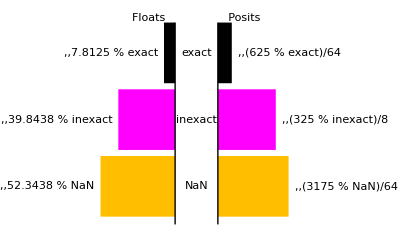

```mathematica
labeler[v_,{s_,j_},{ss_,cj_}]:=Placed[Row[{v "%" cj[[1]]},","],If[s==1,Before,After]]
PairedBarChart[{52.34375,39.84375,7.8125},
{nan/totalp*100,inexact/totalp*100,exact/totalp*100},
ChartBaseStyle->EdgeForm[None],
ChartStyle->{RGBColor[1,0.75,0],Magenta,Black},
ChartLabels->{"NaN","inexact","exact"},
BarSpacing->{30,0,0.1},
Axes->{False, True},
AxesLabel->{"",Row[{Style["Floats",FontFamily->"Arial",18,Green],"                  ",
			Style["Posits",FontFamily->"Arial",18,Magenta]}]},
LabelingFunction->labeler]
```

```mathematica
labeler[v_,{s_,j_},{ss_,cj_}]:=Placed[Row[{v "%" cj[[1]]},","],If[s==1,Before,After]]
PairedBarChart[{1,2,3},{4,5,6},ChartLabels->{"NaN","inexact","exact"},LabelingFunction->labeler]
```

-Graphics-

Float exact values: 7.8125%

Float inexact values: 39.8438%

Float NaN values: 52.3438%

Posit exact values: 9.76563%

Posit inexact values: 40.625%

Posit NaN values: 49.6094%

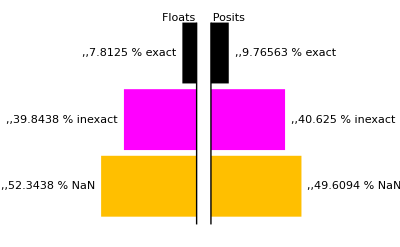

```mathematica
totaln= 2^nbits;
(* Now for Floats *)
logf8=Log2[float8]//FullSimplify;
fnan = Count[logf8, Indeterminate];
fexact = Count[MemberQ[float8,#]&/@logf8, True]-fnan -1;(* Due to -0 *)
fcmpx = Count[logf8, _Complex, Infinity];
fnan = fnan+fcmpx+1;
finexact = Count[MemberQ[float8,#]&/@logf8, False]-fcmpx;
fexact=N[fexact/totaln*100];
finexact=N[finexact/totaln*100];
fnan=N[fnan/totaln*100];
Print[Style[Row[{"Float exact values: "}],"Text"], fexact, "%"];
Print[Style[Row[{"Float inexact values: "}],"Text"], finexact, "%"];
Print[Style[Row[{"Float NaN values: "}],"Text"], fnan, "%"];
(* Now for Posits *)
logp8=Log2[posit8]//FullSimplify;
pnan = Count[logp8, Indeterminate];
pinfty=Count[logp8, Infinity]+ Count[logp8, -Infinity];(* we allow posits to return ±∞ *)
pexact = Count[MemberQ[posit8,#]&/@logp8, True]-pnan+pinfty;
pcmpx = Count[logp8, _Complex, Infinity];
pnan = pnan+pcmpx;
pinexact = Count[MemberQ[posit8,#]&/@logp8, False]-pcmpx-pinfty;
pexact=N[pexact/totaln*100];
pinexact=N[pinexact/totaln*100];
pnan=N[pnan/totaln*100];
Print[Style[Row[{"Posit exact values: "}],"Text"], pexact, "%"];
Print[Style[Row[{"Posit inexact values: "}],"Text"], pinexact, "%"];
Print[Style[Row[{"Posit NaN values: "}],"Text"], pnan, "%"];
(* Plot Bars Graph *)
labeler[v_,{s_,j_},{ss_,cj_}]:=Placed[v "%" cj[[1]],If[s==1,Before,After]]
PairedBarChart[{fnan,finexact,fexact},
{pnan,pinexact,pexact},
ChartBaseStyle->EdgeForm[None],
ChartStyle->{RGBColor[1,0.75,0],Magenta,Black},
ChartLabels->{Placed[{"NaN","inexact","exact"},None]},
Axes->{False, True},
AxesLabel->{"",Row[{Style["Floats",FontFamily->"Arial",18,Green],"     ",
			Style["Posits",FontFamily->"Arial",18,Magenta]}]},
LabelingFunction->labeler]
```